Menyelesaikan persamaan TOV secara numerik

Referensi: 
(http://kugelblitzblackholes.wordpress.com/2015/02/07/numerical-work-in-general-relativity-4-tov-equations/ diakses 25-Juli-2016, pukul 14:38) 
Kodingan Icang

Kode berikut hanya untuk memplot sebuah profil

EOS QUARK Matter based on Extended CIDDM parameter set 
with DI-2500, D1 = 0.46, D2 = 0.3
Energy density as a function of pressure
unit MeV fm^(-3)

#### Start here

```mathematica
ClearAll[ϵ]
```

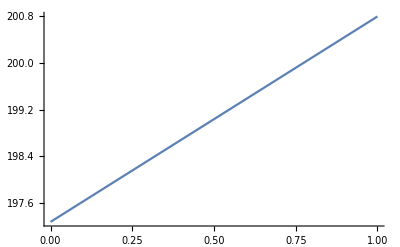

```mathematica
(* Model Neutron Star *)
ϵ[p_]=
(197.282+3.50745 p-0.000267588 p^2+8.79024*10^-8 p^3-1.38896*10^-11 p^4+8.28846*10^-16 p^5);
dϵdp=D[ϵ[p],p];
Plot[ϵ[p],{p,0,1}]
```

```mathematica
(* Model MIT Bag *)
```

```mathematica
ϵ[p_]:=3 p +4B
B:=57
```

```mathematica
eq1[r_]=(4 π r^3 p[r]+m[r])(2GS)/(2 r (r-2 GS m[r]));
(*Persamaan differensial metrik*)
eq2[r_]=-m'[r]+4 π r^2 ϵ[p[r]];(*Persamaan differensial massa*)
eq3[r_]=-p'[r]- eq1[r](ϵ[p[r]]+p[r]) ; (*Persamaan TOV*)
```

```mathematica
GS=1.325*10^-12; (* Konstanta gravitasi *)
MSS= 1.1155 * 10^15; (* Massa matahari *)
r0=10^(-3);rmax=100000.;
MCC=1 *10^-9; (* Massa di pusat *)
PCC=300; (* Tekanan di pusat *)
```

```mathematica
showStatus[status_]:=LinkWrite[$ParentLink,SetNotebookStatusLine[FrontEnd`EvaluationNotebook[],ToString[status]]];
clearStatus[]:=showStatus[""];
clearStatus[]
```

```mathematica
Clear[rStar];
state=First[NDSolve`ProcessEquations[{eq2[r]==0,eq3[r]==0,m[r0]==MCC , p[r0]==PCC,WhenEvent[p[r]==0,{rStar=r,"StopIntegration"}]},{m,p},{r,r0,rmax},Method->{"EquationSimplification"->"Residual"},EvaluationMonitor:>showStatus["p[r] = "<>ToString[CForm[p[r]]]](*,Method->{"EventLocator","Event" :>{p[r]},"EventAction":>Throw[rStar=r,"StopIntegration"]}*)]];
NDSolve`Iterate[state,rmax]
sol=NDSolve`ProcessSolutions[state]
rStar
```

{m→InterpolatingFunction[{{0.001, 10950.9}}, <>],p→InterpolatingFunction[{{0.001, 10950.9}}, <>]}

10950.9

10950.93088835611     2.0116605326862755     1128.     300

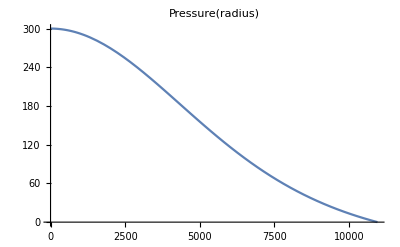

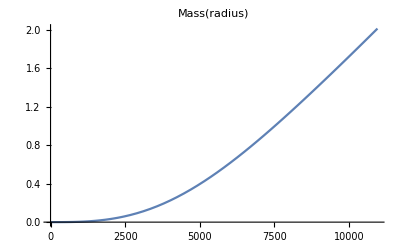

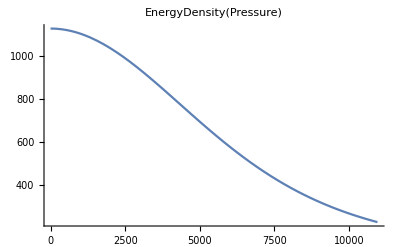

```mathematica
mo[r_]=Evaluate[m[r]/. sol];
po[r_]=Evaluate[p[r]/. sol];
mStar=mo[rStar];
(*Print[rStar,"     ",mStar/MSS,"     ",ϵ[p[r0]],"     ",PCC]*)
Print[FortranForm[rStar],"     ",FortranForm[mo[rStar]/MSS],"     ",ϵ[po[r0]],"     ",PCC]
Plot[{po[r]},{r,r0,rStar},PlotRange->All,PlotLabel->Pressure[radius]]
Plot[{mo[r]/MSS},{r,r0,rStar},PlotRange->All,PlotLabel->Mass[radius]]
Plot[{ϵ[po[r]]},{r,r0,rStar},PlotRange->All,PlotLabel->EnergyDensity[Pressure]]
```

Mencoba membuat iterasi masih secara manual untuk melihat satu profil. 

Script yang di atas harus tetap dijalankan terlebih dahulu. Jika plot di atas sudah benar, baru bisa menjalankan iterasi.

Data di bawah yang dapat dikopi ke file *.txt adalah pada kolom:
1. Radius bintang dalam satuan meter
2. Massa bintang dalam satuan massa matahari
3. Tekanan di inti bintang
4. Densitas energi di inti bintang

Kendala: masih belum bisa menghentikan iterasi saat massa mulai turun sementara radius bintang terus meningkat

```mathematica
(* Bikin nama file untuk dibaca di mathematica *)
fname=FileNameJoin[{NotebookDirectory[],"TOV-GR-rStar-VS-Mass.txt"}]; 
(* Data keluaran:
(rStar/1000)     (mStar) *)
gname=FileNameJoin[{NotebookDirectory[],"TOV-GR-ec-VS-Mass.txt"}]; 
(* Data keluaran:
 EDC     (mStar)  *)
hname=FileNameJoin[{NotebookDirectory[],"TOV-GR-ec-VS-rStar.txt"}]; 
(* Data keluaran:
 EDC     (rStar)  *)
```

```mathematica
n=1;maxit=600;
f=OpenWrite[fname,FormatType->OutputForm];
g=OpenWrite[gname,FormatType->OutputForm];
h=OpenWrite[hname,FormatType->OutputForm];
While[n<maxit,{
 PCC=10^0 *n;
Clear[rStar];
state=First[NDSolve`ProcessEquations[{eq2[r]==0,eq3[r]==0,m[r0]==MCC , p[r0]==PCC},{m,p},{r,r0,rmax},Method->{"EventLocator","Event" :>{p[r]},"EventAction":>Throw[rStar=r,"StopIntegration"]}]];
NDSolve`Iterate[state,rmax];sol=NDSolve`ProcessSolutions[state];
mo[r_]=Evaluate[m[r]/. sol];
po[r_]=Evaluate[p[r]/. sol];
mStar=N[mo[rStar]];
ϵ0=N[ϵ[PCC]];
(* Membuat data keluaran yang dapat dikopi ke sebuah *.txt yang diplot dengan gnuplot *)
If[rStar∈Reals,
Write[f,N[(rStar/1000)]," ",N[(mStar/MSS)]]
Write[g,ϵ0," ",N[(rStar/1000)]]
Write[h,ϵ0," ",N[(mStar/MSS)]]
,]
(* Print[rStar,"     ",mStar,"     ",ϵ[po[r0]],"     ",PCC] *)
n++}]
Close[f]; 
Close[g];
Close[h];
```

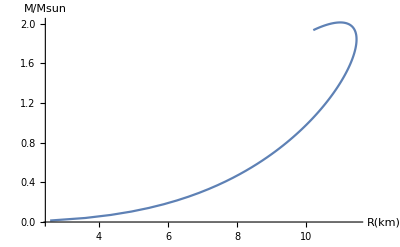

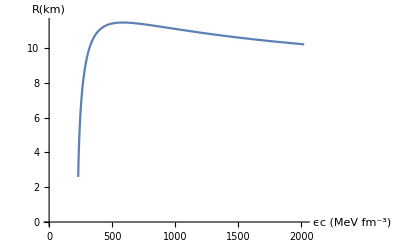

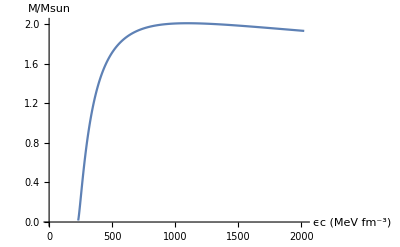

```mathematica
(* Data tersebut diplot lagi di sini *)
f=OpenRead[fname];
dataf=ReadList[f,{Number,Number}];
Close[f];
g=OpenRead[gname];
datag=ReadList[g,{Number,Number}];
Close[g];
h=OpenRead[hname];
datah=ReadList[h,{Number,Number}];
Close[h];
ListLinePlot[{dataf},PlotRange->All,AxesLabel->{"R(km)","M/Msun"}]
ListLinePlot[{datag},PlotRange->{0,11.46},AxesLabel->{"ϵc (MeV fm^-3)","R(km)"}]
ListLinePlot[{datah},PlotRange->{0,2.02},AxesLabel->{"ϵc (MeV fm^-3)","M/Msun"}]
```

```mathematica
(57*197^3)^(1/4)//N
```

144.484